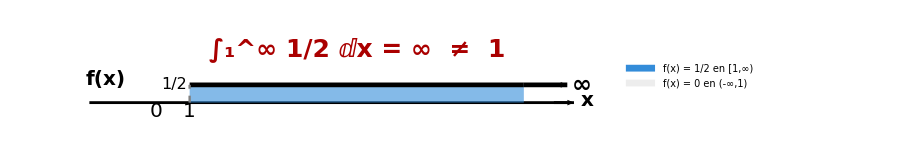

```mathematica
xMax=11;
alturaDensidad=1/2;

colorArea=RGBColor[0.2,0.55,0.85];
colorCero=RGBColor[0.93,0.93,0.93];

grafico=Graphics[{
(*eje x,con flecha hacia+infinito*)
Black,Thickness[0.003],Line[{{-2,0},{xMax+1.3,0}}],Arrowheads[0.02],Arrow[{{xMax+0.9,0},{xMax+1.5,0}}],

(*área bajo la densidad para x>=1 (parte visible)*)
colorArea,Opacity[0.6],Rectangle[{1,0},{xMax,alturaDensidad}],

(*nivel f(x)=1/2,prolongado con flecha hacia el infinito*)
Black,Opacity[1],Thickness[0.005],Line[{{1,alturaDensidad},{xMax,alturaDensidad}}],Arrow[{{xMax,alturaDensidad},{xMax+1.3,alturaDensidad}}],Text[Style["∞",24,Bold],{xMax+1.75,alturaDensidad}],

(*marca en x=1*)
Gray,Dashed,Thickness[0.0025],Line[{{1,0},{1,alturaDensidad}}],Black,Text[Style["1",20],{1,-0.25}],Text[Style["0",20],{0,-0.25}],

(*etiquetas*)
Text[Style["x",20,Bold],{xMax+1.9,0.05}],
Text[Style["f(x)",20,Bold],{-1.5,alturaDensidad+0.15}],
Text[Style["1/2",16],{0.55,alturaDensidad}],
(*conclusión:la integral diverge*)
Text[Style[Row[{HoldForm[Integrate[1/2,{x,1,Infinity}]]," = ","∞","  ≠  1"}],25,Bold,Darker[Red]],{(1+xMax)/2.,alturaDensidad+1}]},PlotRange->{{-2.3,xMax+2.3},{-1,alturaDensidad+2}},ImageSize->680];

imagenFinal=Legended[grafico,SwatchLegend[{colorArea,colorCero},{"f(x) = 1/2  en  [1,∞)","f(x) = 0  en  (-∞,1)"},LabelStyle->Directive[FontSize->16],LegendMarkerSize->20]];

imagenFinal
```

```mathematica
Export["prob_quesada_2_3_a.png",imagenFinal,Background->None,ImageResolution->1200];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["prob_quesada_2_3_a.png"]]]
```